```mathematica
json=Import["/tmp/json","RawJSON"];
```

```mathematica
Length@json
```

31036

```mathematica
json
```

```mathematica
data=json//#["charsCount"]&/@#&;
```

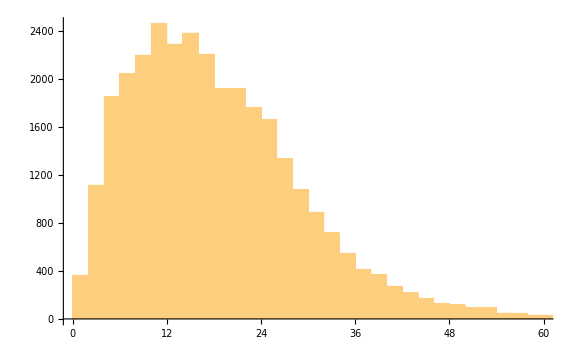

```mathematica
Histogram[data,1000,"Count",ImageSize->Large,Ticks->{Table[n,{n,0,64,4}], Automatic}]
```

```mathematica
data=ParallelMap[FromUnixTime@#["time"]&,json]
```

```mathematica
Manipulate[
DateHistogram[data,Quantity[days,"Days"],"Count",ImageSize->Large,DateReduction->None,DateTicksFormat->{"Year",".","Month"}],
{days,1,100}
]
```